# A Machine Learning Analysis of Halting in the SKI Combinator Calculus

## Euan Ong

## Abstract

Much of machine learning is driven by the question: can we learn what we cannot compute? The learnability of the halting problem, the canonical undecidable problem, to arbitrarily high accuracy for Turing machines was proven by Lathrop (Lathrop, 1996). The SKI combinator calculus can be seen as a reduced form of the untyped lambda calculus, which is Turing-complete (Turing, 1937); hence, the SKI combinator calculus forms a universal model of computation. In this vein, we analyse the growth and halting times of SKI combinator expressions, estimate the probability of an SKI combinator expression halting after a given number of steps and investigate the feasibility of a machine learning approach to predicting whether a given SKI combinator expression is likely to halt.

## SK Combinators

<Write about SKI combinators and what halting means - nb, we are not trying to *solve* the *halting problem* which is undecidable. Talk about https://www.ics.uci.edu/~rickl/publications/1996-icml.pdf>
https://en.wikipedia.org/wiki/Unlambda

```mathematica
k[x_][y_]:=x
```

```mathematica
s[x_][y_][z_]:=x[z][y[z]]
```

```mathematica
s[k][s][k]
```

k

### Rules

```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]}
```

{k[x_][y_]:>x,s[x_][y_][z_]:>x[z][y[z]]}

```mathematica
s[k][s][k]/.SKRules
```

k[k][s[k]]

```mathematica
k[k][s[k]]/.SKRules
```

k

```mathematica
x = s[k][s][k]
```

s[k][s][k]

```mathematica
y = x/.SKRules
```

k[k][s[k]]

```mathematica
y
```

k[k][s[k]]

```mathematica
x
```

s[k][s][k]

s[k][s][k]==s[k][s]

```mathematica
ClearAll[s,k,x,y,z]
```

```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]};
SKEvaluate[expr_]:=
NestList[#1/.SKRules&,expr,50]
```

```mathematica
SKEvaluate[s[k][s][k]]
```

{s[k][s][k],k[k][s[k]],k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k,k}

```mathematica
{s[k][s][k]}
```

{s[k][s][k]}

```mathematica
expr = s[s[s]][s][s][s]
```

s[s[s]][s][s][s]

```mathematica
y = Characters/@ToString/@SKEvaluate[expr]
```

```mathematica
x=s[s[s[s]][s]][s[s[s[s]][s]]]
```

s[s[s[s]][s]][s[s[s[s]][s]]]

```mathematica
Characters[y]
```

{s,[,s,[,s,[,s,],],[,s,],],[,s,[,s,[,s,[,s,],],[,s,],],]}

```mathematica
SKColourTable = Table[{x,y}->Blue,{x,11},{y,11}]
```

```mathematica
abc = Flatten[SKColourTable,1]
```

### Rasterization - add examples

```mathematica
SKRasterize[func_]:=SKRasterize[func,10];
SKRasterize[func_,n_]:=Module[{SKRules,SKEvaluate,SKArray,SKGrid},
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]};
SKEvaluate[expr_]:=NestList[#1/.SKRules&,expr,n];
SKArray[expr_]:=Characters/@ToString/@SKEvaluate[expr];
SKGrid[exp_]:=ArrayPlot[SKArray[exp],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}];
SKGrid[func]
]
```

```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]};
SKEvaluate[expr_,n_]:=NestList[#1/.SKRules&,expr,n];
SKEvaluate[expr_]:=SKEvaluate[expr,10];
SKArray[expr_]:=SKArray[expr,10];
SKArray[expr_,n_]:=Characters/@ToString/@SKEvaluate[expr,n];
SKGrid[exp_]:=SKGrid[exp,10];
SKGrid[exp_,n_]:=ArrayPlot[SKArray[exp,n],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}];
SKRasterize[func_]:=SKRasterize[func,10];
```

```mathematica
SKRasterize[func_,n_]:=SKGrid[func,n]
```

```mathematica
SKLengths[exp_,n_]:=StringLength/@ToString/@SKEvaluate[exp,n];
```

```mathematica
SKRasterize[s[s][k][s[s[s][k]]][k]]
```

-Graphics-

```mathematica
SKFuncs = {s[s[s]][s][k][k],s[s[s]][s][s][s],s[s[s]][s][s][s][k],s[s][s][s[s[s]]][s],s[s[s]][s][s][s][s],s[s[s]][s][s][s][s],s[s][s][s[s[s[s]]]][k],s[s][k][s[s[s]]][s][k],s[s][s][s[s[s]]][s][k],s[s][s][s[s]][s][s[k]],s[s[s[s][s]]][s][s][k],s[s][k][s[s[s][k]]][k]}
```

{s[s[s]][s][k][k],s[s[s]][s][s][s],s[s[s]][s][s][s][k],s[s][s][s[s[s]]][s],s[s[s]][s][s][s][s],s[s[s]][s][s][s][s],s[s][s][s[s[s[s]]]][k],s[s][k][s[s[s]]][s][k],s[s][s][s[s[s]]][s][k],s[s][s][s[s]][s][s[k]],s[s[s[s][s]]][s][s][k],s[s][k][s[s[s][k]]][k]}

```mathematica
SKRasterize/@SKFuncs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Random SK combinators ()

### Investigating growth of SK combinators

SKLengths generates a table of length of combinator

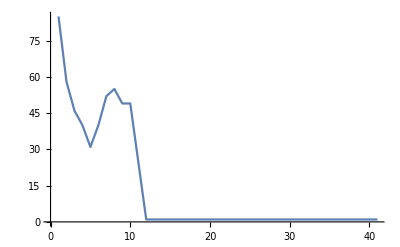

```mathematica
ListLinePlot[SKLengths[k[k[k[k[s[s[s]]]][s]][k[s][k]][s[k]][k]][k[s[k[k]][s]][k[k]][k]][s[k[k[k]]]][s[s]][s],40]]
```

```mathematica
Column[Table[{x=RandomSKExpr[5],SKRasterize[x]},100]]
```

```mathematica
SKRasterize[k[s[s[k[s][k[k]][s]][s[s[s]]][s[k]][s]]][k[k[s[k]]]][s[s]][s],20]
```

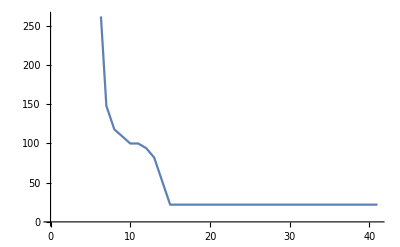
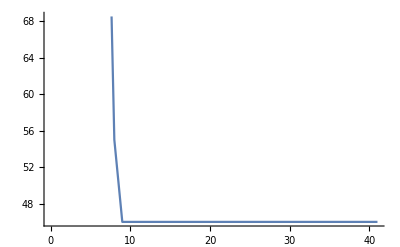
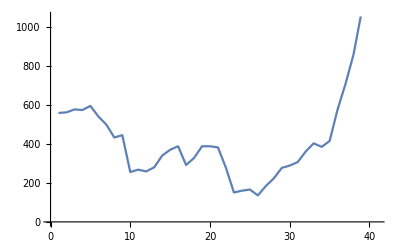
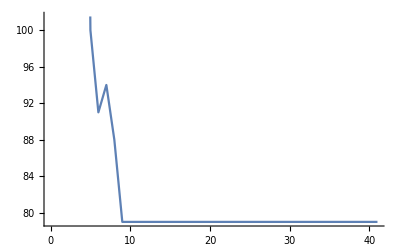
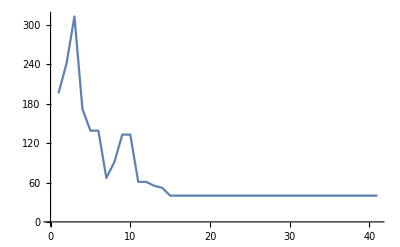
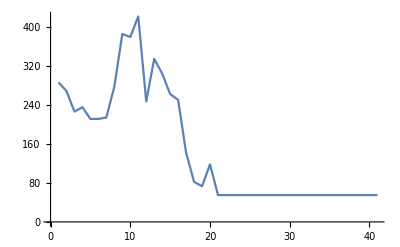
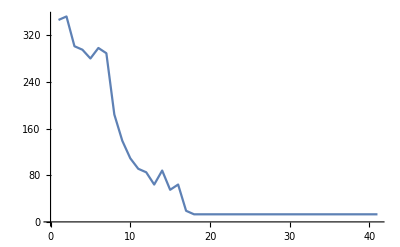
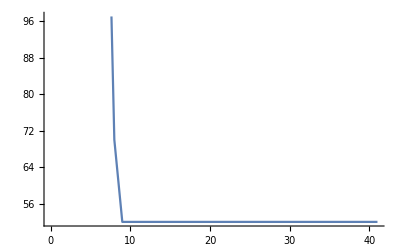

```mathematica
exprs = Table[RandomSKExpr[10],100];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,100}]]
```

```mathematica
ImageCollage[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

Some halt, some do not. (haven’t seen a cyclical one yet) --> linear/exponential.
Assumptions: If length stays constant, it has halted. Dataset: SK combinators with depth 10
P(halts by 20|doesn’t halt by 10) = ? P(halts by 30|doesn’t halt by 20

```mathematica
exprs = Monitor[Table[RandomSKExpr[10],{n,100}],n];
```

```mathematica
lengths = Monitor[Table[SKLengths[exprs[[n]],40],{n,100}],n];
```

$Aborted

```mathematica
HaltIf[n_,list_]:=SameQ[list[[n]],list[[n-1]]]
```

```mathematica
HaltBy[n_,lens_]:=Count[lens,x_/;HaltIf[n,x]==True]
```

```mathematica
ListLinePlot[Table[HaltBy[n,lengths],{n,0,35}]]
```

-Graphics-

Number that have ‘constant length’ after every 5 iterations (c.f. nuclear half life?)

Number that have halted after every 5 iterations (checking for actual halting)

```mathematica
Table[HaltBy[n,lengths]-HaltBy[n-5,lengths],{n,5,40,5}]
```

{27,19,16,15,8,5,0,0}

```mathematica
exprs = Monitor[Table[RandomSKExpr[10],{n,100}],n];
```

```mathematica
lengths = Monitor[Table[SKEvaluate[exprs[[n]],50],{n,100}],n];
```

```mathematica
Monitor[ListLinePlot[Table[HaltBy[n,lengths],{n,0,50}]],n]
```

Part::partw: Part 42 of {s[s[s[s[s[k[s[«1»][«1»]][k[«1»]][k[«1»]]]][k[k]][k]]][k[s[k[k[k[«1»]]]]][s]][s[k[s[s[s[«1»][«1»]][k[«1»]]]]][s]][k[k][s[k[k[s][s]][s[s]]]][s[s][k]][s[s]][k]][k[s[k[s[s]]]]][s[s][s[s]][k]][k[k[k[s]]]][s[k]]],«39»,s[k]} does not exist.

Part::partw: Part 42 of {k[s[k[k[s[s][s[k[«1»][«1»]]][k[s[«1»][«1»][«1»][«1»]]]][s[s[k[«1»][«1»][«1»][«1»]]][s[k[«1»]]][s[s]][k]]]]][s[s]][k],s[k[k[s[s][s[k[s[«1»]][k[«1»]]]][k[s[s[«1»]][s[«1»][«1»]][k[«1»][«1»]][s[«1»]]]]][s[s[k[s][k[«1»][«1»]][s[«1»]][s]]][s[k[k]]][s[s]][k]]]][k],«38»,s[k[s[k[s[k][s[s]]]][s[s[k[s[«1»][«1»]]]][k[s[k][s[«1»]]]]]]][k]} does not exist.

Part::partw: Part 42 of {k[s[k[s[k[s[k[«1»]]][s[s[«1»][«1»]][k[«1»]][k]]]]]][s],s[k[s[k[s[k[k[«1»]]]][s[s[k[«1»][«1»]][k[«1»][«1»]]][k[s]][k]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],«27»,s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]],s[k[s[s[k[k[k]]]]]]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
SKHalt[expr_,limit_]:=Module[{evaluate},
evaluate = SKEvaluate[expr,limit];
HaltIf[limit,evaluate]
]
```

```mathematica
SKHalt[k[s[s[k[s][k[k]][s]][s[s[s]]][s[k]][s]]][k[k[s[k]]]][s[s]][s],10]
```

False

#### Training #1

```mathematica
exprs = Monitor[Table[RandomSKExpr[10],{n,1000}],n];
```

```mathematica
lengths = Monitor[Table[exprs[[n]]-> SKHalt[exprs[[n]],40],{n,1000}],n];
```

```mathematica
Count[Values[lengths],False]
```

```mathematica
l2 = lengths
```

```mathematica
l2[[1]][[2]]
```

True

```mathematica
NoHalt = Select[lengths,#[[2]]==False&]
Halt = Select[lengths,#[[2]]==True&]
HaltTrain = RandomSample[Halt,Length[NoHalt]]
TrainingData = Join[HaltTrain,NoHalt]
TrainingData/.Rule->List
TrainingData2 = Table[ToString[TrainingData[[n]][[1]]]-> TrainingData[[n]][[2]],{n,1,Length[TrainingData]}];
```

```mathematica
Halt = Select[lengths,#[[2]]==True&]
```

```mathematica
HaltTrain = RandomSample[Halt,Length[NoHalt]]
```

```mathematica
TrainingData = Join[HaltTrain,NoHalt]
```

```mathematica
TrainingData/.Rule->List
```

```mathematica
TrainingData2 = Table[ToString[TrainingData[[n]][[1]]]-> TrainingData[[n]][[2]],{n,1,Length[TrainingData]}];
```

```mathematica
Classify[TrainingData]
```

```mathematica
ClassifierFunction[…]
HaltClassifier1 = Classify[TrainingData2]
```

ClassifierFunction[…]

ClassifierFunction[…]

```mathematica
ClassifierFunction[…][k[s[s[k[s][k[k]][s]][s[s[s]]][s[k]][s]]][k[k[s[k]]]][s[s]][s]]
```

#### Best classifier so far:

```mathematica
HaltClassifier1["s[s[s]][s][s][s][k]"]
```

True

```mathematica
TestClassifier[c_]:=Module[{x,y,z},
x=RandomSKExpr[10];
y = c[ToString[x]];
z = SKPlot[x,40];
Return[{y,z,MemberQ[TrainingData2,x]}]
]
```

```mathematica
TestClassifier[HaltClassifier1]
```

{False,-Graphics-}

```mathematica
MemberQ[TrainingData2,
```

```mathematica
TestClassifier[HaltClassifier1]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier1]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier1]
```

{True,-Graphics-}

```mathematica
TestClassifier[HaltClassifier1]
```

{True,-Graphics-}

```mathematica
TestClassifier[HaltClassifier1]
```

{True,-Graphics-}

```mathematica
TestClassifier[HaltClassifier1]
```

{True,-Graphics-}

```mathematica
SKGrid[k[s[k[k[k[k[s[s[k[k[k[k][s[s[k[k[s[s][k[k[k][k[k[s[k]]]]][k[k]][s]]]]][k[s]]]][k[s[k[k][k[s[k[s[s][s[s]]]][s[s[k]]]][k]]][s[s[k[k]]]][k[k]]]][s[k[s[s[k][s[k][k]][s[k]]]][k[s[k]][k]]][s[k]][k]]][s[k[s]][k]][k[k[k]]]][k]]]]]]][k[s[s[k[s[s]]]]][s]]][k[s]]]]
```

-Graphics-

```mathematica
GenerateTable[depth_,iterations_,number_]:=Module[{exprs},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[exprs[[n]]-> SKHalt[exprs[[n]],iterations],{n,number}],n];
Return[lengths]
]
```

```mathematica
Monitor[Flatten[Table[GenerateTable[n,40,200],{n,1,10}]],n]
```

{k[s]→True,s[k]→True,1997,s[k[k[s[k[k[s[k[s[s[s[k][k[k[k[s[k[s[k[s[k[s][s[s[k]][k[s]][s]]][s[s][s]][k[k]]]]][k[k[s][k[s]][s]][s[s[k]][k]][s[k]][k]]]]]]][s[s[k[k[s[k[k[s[k]][s[k[k]]]]]]][s[k[k[s][s]]][k]][s[k[s]][s]]]]]]][s[k][k[s]][s]][s[s[s]]][s[k]][k]]]]]][s[k][k[s[s]][k]][s[k]][s]]]][k[k]]]→True}
 |  |  |  |

#### Try with more data...

```mathematica
LargeTrainingData = {{{k[s]->True,s[k]->True,1997,s[k[k[s[k[k[s[k[s[s[s[k][k[k[k[s[k[s[k[s[k[s][s[s[k]][k[s]][s]]][s[s][s]][k[k]]]]][k[k[s][k[s]][s]][s[s[k]][k]][s[k]][k]]]]]]][s[s[k[k[s[k[k[s[k]][s[k[k]]]]]]][s[k[k[s][s]]][k]][s[k[s]][s]]]]]]][s[k][k[s]][s]][s[s[s]]][s[k]][k]]]]]][s[k][k[s[s]][k]][s[k]][s]]]][k[k]]]->True}}, {{{, , , , }}}}
```

```mathematica
LargeTrainingData = DeleteDuplicates[LargeTrainingData]
```

{k[s]→True,s[k]→True,1560,s[k[k[s[k[k[s[k[s[s[s[k][k[k[k[s[k[s[k[s[k[s][s[s[k]][k[s]][s]]][s[s][s]][k[k]]]]][k[k[s][k[s]][s]][s[s[k]][k]][s[k]][k]]]]]]][s[s[k[k[s[k[k[s[k]][s[k[k]]]]]]][s[k[k[s][s]]][k]][s[k[s]][s]]]]]]][s[k][k[s]][s]][s[s[s]]][s[k]][k]]]]]][s[k][k[s[s]][k]][s[k]][s]]]][k[k]]]→True}
 |  |  |  |

```mathematica
Length[LargeTrainingData]
```

1563

#### ...nope, doesn’t work

```mathematica
LargeTrainingData2=Table[ToString[LargeTrainingData[[n]][[1]]]->LargeTrainingData[[n]][[2]],{n,1,Length[LargeTrainingData]}];
```

```mathematica
LargeTrainingData2[[1]]
```

k[s]→True

```mathematica
LargeClassify = Classify[LargeTrainingData2]
```

ClassifierFunction[…]

```mathematica
LargeClassify["s[s][s][s[s[s]]][s][s][s][s][s]"] (* halts *)
```

False

#### Which in largetrainingdata don’t halt?

```mathematica
NoHaltLarge2= Select[LargeTrainingData2,#[[2]]==False&];
```

```mathematica
NoHaltLarge2[[5]]
```

k[s[k[s][s[s[s[s[s]][s]]][k]][k[s][k]][k[s]][s]][s[k[s[k[k]]]]][s[s][k[k]][s]][k[k[s]]][s[k]]]→False

```mathematica
Length[NoHaltLarge2]
```

99

```mathematica
HaltLarge2= Select[LargeTrainingData2,#[[2]]==True&];
```

```mathematica
Length[HaltLarge2]
```

1464

#### ok... many halt.

```mathematica
HaltTrainLarge2=RandomSample[HaltLarge2,Length[NoHaltLarge2]];
```

```mathematica
TrainLarge2Sample = Join[HaltTrainLarge2,NoHaltLarge2];
```

```mathematica
TrainLarge2Sample[[-1]]
```

k[k[s[s[s]][s[k[k[k][s[s[k][s[k[k]][s]][k[k]]]]][s[k[s[k]]]][s[s]][s]][s[k[k[s[s[k[k][s[s][s]]]]]][k[s[k]]]][s]][k[k[s[s[s[s]]]]][k[k]][k]][k[s[s[s]]]][s[s[s[k]]]][s[s]][k]][k[k[s[k[k[k[k[s[s][k[s]][s]][k[s][s]][s[k]]]][k[s][k[k]][k]][s[s[k[s]]]]]]][s[k[k]][k[k]][k]][k[s[s[s[k[k]][k]]]]]][k[s]][k]][s[k[s[k[s[s[k[k[s[k]][s]]]][k]]]][s[s]]]][s[k[s[k[k[s][k]][k[k]]]][k[k][s]][s[k]]]][k[s[s][k]][s[s]][s]]][k[s]]]→False

```mathematica
Large2Classify = Classify[TrainLarge2Sample]
```

ClassifierFunction[…]

```mathematica
Large2Classify["s[s[s[k[s[s[k[s[k][s]]][k]]][k[k]][k]]]][s[s]][s]"]
```

True

#### Retry small dataset

#### Training #2

```mathematica
exprs = Monitor[ParallelTable[RandomSKExpr[10],{n,5000}],n];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
lengths = Monitor[ParallelTable[exprs[[n]]-> SKHalt[exprs[[n]],40],{n,5000}],n];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

```mathematica
LaunchKernels[]
```

SubKernels`LocalKernels`LaunchLocal::nolic2: Could not provide a subkernel license.

SubKernels`LocalKernels`LaunchLocal::somefail: 2 of 2 kernels failed to launch.

{}

```mathematica
gridexprs = Monitor[ParallelTable[SKGrid[exprs[[n]]],{n,1,Length[exprs]}],n];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
exprs[[1]]
```

k[s[k[k[k[k[s[s[k][k[s[s[s[s[k[k[k[k[s[s[k[s[k[s[s[s[k[k[s]]]]][k[s[s[k[k[s]]]]][k]]]]]][s[k[k[k]][s[k]]]][s[k[k[k[k[k]][s]]]]][k[k[k[k]]]][s[s]]]][s[k[s[k[s[s]]]]]][s[s[s][k[k][k]][k[k]]]][k[s[s][s[k]]]]][k[s]]]]]][s[s[k[s[k][s]][k[s]][k]]][s[k]][k]][k[k[s[k[k]][k]][k[k]]]]]]]]][s[k[k[s][k[k[s[k[k[k[s][s]][k[s]][k]]]]]][s[k[s[s]]]][k[k[s[s]]]]]]]]]]]]]

```mathematica
Count[Values[lengths],False]
```

903

```mathematica
NoHalt = Select[lengths,#[[2]]==False&];
Halt = Select[lengths,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
TrainingData = Join[HaltTrain,NoHalt];
TrainingData/.Rule->List;
TrainingData2 = Table[ToString[TrainingData[[n]][[1]]]-> TrainingData[[n]][[2]],{n,1,Length[TrainingData]}];
```

```mathematica
HaltClassifier2 = Classify[TrainingData2]
```

ClassifierFunction[…]

#### Testing

```mathematica
TestClassifier[HaltClassifier2]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{False,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

```mathematica
TestClassifier[HaltClassifier2]
```

{True,-Graphics-,False}

#### Other classifiers

```mathematica
exprs[[1]]
```

Part::partd: Part specification exprs⟦1⟧ is longer than depth of object.

exprs⟦1⟧